# Diffie-Hellman Algorithm

Diffie-Hellman Algorithm is an algorithm of securely exchanging cryptographic keys in the modern internet to ensure the Transport Layer Security.

Siyi(Raymond) Guo, Jun. 24,  2018

Modern internet security involves the usage of RSA. In particular, we use a pair of Private and Public key to encrypt and decrypt the message. However, the disadvantage of RSA is that if one part lost its private key, all the past communication can be decrypted. Therefore we need to find a way that both parties can share the information, and past communication can still be protected if one party lost its private key. And this is the motivation for Diffie Hellman Algorithm, an algorithm that allow both parties to calculate a shared key without having to ever explicitly communicate the shared key.

## Simple Illustration

The idea behind Diffie-Hellman is that, both party have a common tool, each of them adding its own secret to the tool that explicitly communicate the new message over the internet. And we can find a tricky way that both party can recover the received message with its own secret.

Here is a visualization of how the algorithm works.

```mathematica
SetDirectory[NotebookDirectory[]];
Import["illustration.png"]
```

-Graphics-

## A small example of application

To illustrate the algorithm, here is a example.

Alice and Bob Started with a common paint.

This is a pair of integers {g,p}. p is a prime, and g is a primitive root modulo p.  For now, just think primitive root modulo as a special connection between g and p such that made them a good friends.

```mathematica
g = 5;
p = 23;
```

Now Alice holding the private key a:

```mathematica
a = 5;
```

To generate the message that will be sent to Bob is g^a mod p:

```mathematica
AliceSecret= Mod[g^a, p]
```

20

And Bob has the private key b:

```mathematica
b = 3;
```

The generated message that Bob will send to Alice is g^b mod p:

```mathematica
BobSecret = Mod[g^b, p]
```

10

Now Alice and Bob will sent g, p, AliceSecretToBob(g^a mod p), BobSecretToAlice(g^b mod p) to each other in PLAIN TEXT.

Alice to Bob:

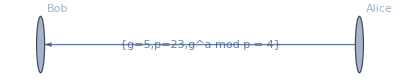

```mathematica
Graph[{Labeled["Alice"->"Bob",{"g=5","p=23", "g^a mod p = 4"}]}, VertexLabels->"Name"]
```

Bob to Alice:

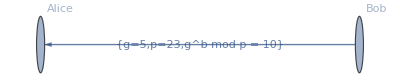

```mathematica
Graph[{Labeled["Bob"->"Alice",{"g=5","p=23", "g^b mod p = 10"}]}, VertexLabels->"Name"]
```

After the Communication, now Alice has g, p, a(Alice’s private key) and BobSecrect:

```mathematica
{"g"->g, "p"->p, "a"->a,"BobSecret"->BobSecret}
```

{g→5,p→23,a→5,BobSecret→10}

We can then calculate the Common Secret: BobSecret^a mod p

```mathematica
AliceReceivedCommonSecret = Mod[BobSecret^a , p]
```

19

So how about Bob? he now has g, p, b(Bob’s private Key), and AliceSecret:

```mathematica
{"g"->g, "p"->p, "b"->b,"AliceSecret"->AliceSecret}
```

{g→5,p→23,b→3,AliceSecret→20}

We can therefore Calculate the Common Secret: AliceSecret^b mod p

```mathematica
BobReceivedCommonSecret = Mod[AliceSecret^b, p]
```

19

We can find What Alice Decoded equal to What Bob Decoded, and therefore, this number become their Common Secret.

```mathematica
AliceReceivedCommonSecret == BobReceivedCommonSecret
```

True

And this Common Secret can be used as a key for the Symmetric Encryption to transfer the information, without the concern of key being exposed at the beginning of the Communication.

## The Mathematical induction

Here is a formula proof of how Alice and Bob end up with the same Result

Alice And Bob have:

```mathematica
ClearAll[g,p,a,b];
"Alice"->{"Common Pair"->{g,p}, "PrivateKey"->a}
"Bob" ->{"Common Pair"->{g,p}, "PrivateKey"->b}
```

Alice→{Common Pair→{g,p},PrivateKey→a}

Bob→{Common Pair→{g,p},PrivateKey→b}

Alice and Bob Encrypt Message:

```mathematica
A=Mod[g^a,p]
B=Mod[g^b, p]
```

Mod[g^a,p]

Mod[g^b,p]

But in fact, when Alice use B^a mod p and Alice use A^b mod p to decrypt is basically doing:

Alice

```mathematica
Mod[B^a, p] == Mod[g^(ab), p] == Mod[g^(ba), p] == Mod[A^b, p];
```

## Why it is secure?

Modern Cryptography are all based on the problem that considered to be Mathematically Hard. For example, RSA based on the problem of  factorizing the prime.

Whereas Diffie-Hellman is based on solving the discrete log

THe discrete log problem is simple:

Suppose there is a secret number a:

```mathematica
a = 5;
```

And the only clue you have is g, p, and g^a mod p:

```mathematica
g = 5; p = 23; "g^a mod p"->Mod[g^a, p]
```

g^a mod p→20

How can you find the value of x, such that g^x mod p == g^a mod p?

To do that, you need to go through all possible combination value x from 1 to p

```mathematica
ResultListofAllPosibbleValue = Map[Mod[g^#, p]&, Range[p - 1]]
```

{5,2,10,4,20,8,17,16,11,9,22,18,21,13,19,3,15,6,7,12,14,1}

And you spotted that 20, at the fifth position, equal to the value you get on and, which is g^a mod p  = 20

Therefore, the value of x = 5 = a

```mathematica
x = 5;
Mod[g^x, p] == Mod[g^a, p]
```

True

So you have successfully recover a from g, p, and Mod[g^a, p] , by looking at the position of Mod[g^a,p] in that list.
Therefore, we can see, the problem of solving discrete log is equivalent to the problem of :

```mathematica
Given a sequence of number that is nearly in random order, can you find the targeted number’s position in this sequence. ;
```

However, find the position of a particular number in a list is not a easy task. Because the list generated from Mod is almost at random order.

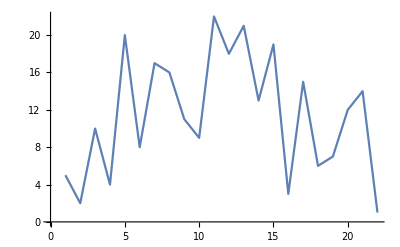

```mathematica
ListLinePlot[ResultListofAllPosibbleValue]
```

Moreover, the length of the list that you are going to look up is relates to the choice on p.

In particular, the number you need to look up is equal to p-1

```mathematica
Length @ ResultListofAllPosibbleValue == p -1
```

True

In practice, the value of g is usually small integer, like 2 or 3. However, the selection of p is usually a prime with hundreds of digits.  Says:

```mathematica
g = 2;
p = RandomPrime[{10^400, 10^401}]
```

62166362167977159598307859909354498207589031649708285199616497129070424340662862498463476867343144321998540170516208798864975732396260013799534464447842854202119064930601121882221281016095346588929180373058899450449703181258182508687601467674422931572792533224269981813535953647057543934359713180757976862869147791060956293393088239689646087055374666631047268517100407964602911862210851224587747022067

And Lets say the private key and the Secret  is :

```mathematica
a = 6;
secret = Mod[g^a, p]
```

64

However, if you only know g, p, the secret(Mod[g^a,p]), it gonna to be hard to recover a from it.

Try the following command (Endless Loop WARNING):

```mathematica
i = 1;
While[i < p, If[Mod[g^i,p] == a, Print[i]];i++]
```

You can see the program runs into endless loop. In fact, if we use p such that is a prime with more than 600 digits, the even the fastest computer on Earth will not able to recover a, given g, p and the value of g^a mod p.

However, Such encryption can be still cracked by a quantum computer.

## Author contact information

guosiyi1997@outook.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)